```mathematica
quarticmatchings={
Lambda1== (1+tanb^2)/(2*(1+tana^2)*v^2)*(mH^2+M12*tanb+tana^2(mh^2+M12*tanb)),
Lambda2==(1+tanb^2)/(2*(1+tana^2)*tanb^3*v^2)*(M12*tana^2+M12+tanb*(mh^2+mH^2tana^2)),
Lambda3==1/((1+tana^2)*tanb*v^2)*(-mh^2*tana+2*mHp^2*(1+tana^2)*tanb-mh^2*tana*tanb^2+mH^2*tana*(1+tanb^2)+M12*(1+tana^2)(1+tanb^2)),
Lambda4==1/(tanb*v^2)*(-M12+mA^2*tanb-2*mHp^2*tanb-M12*tanb^2),
Lambda5==1/(tanb*v^2)*(-M12-mA^2*tanb-M12 tanb^2)
};
```

```mathematica
sol1= Solve[quarticmatchings,{tanb,mH,M12,mHp,mA}];
Put[sol1,"solsav1"]
```

```mathematica
sol1[[1]]//Length
```

5

```mathematica
Put[soltest,"solsavet"]
```

```mathematica
sol=Get["solsave"];
soltest=sol[[1,1]]
```

tanb→-√(-(«22»+4 Lambda2 Lambda5 v^4+2 Lambda3 Lambda5 v^4+2 Lambda4 Lambda5 v^4+Lambda5^2 v^4)/(3 (mh^2 mH^2-2 Lambda2 mh^2 v^2-2 Lambda2 mH^2 v^2+4 Lambda2^2 v^4))-(2^(1/3) (3 («1») («1»)-(«1»)^2))/(3 («5»+4 («7»)^2 v^4) («1»)^(1/3))+(«1»)^(1/3)/(3 2^(1«1»«1») (mh^2 mH^2-2 Lambda2 mh^2 v^2-2 Lambda2 mH^2 v^2+4 Lambda2^2 v^4)))

```mathematica
sol//Length
```

24

```mathematica
sol[[1,1]]
```

tanb→-√(-(«22»+4 Lambda2 Lambda5 v^4+2 Lambda3 Lambda5 v^4+2 Lambda4 Lambda5 v^4+Lambda5^2 v^4)/(3 (mh^2 mH^2-2 Lambda2 mh^2 v^2-2 Lambda2 mH^2 v^2+4 Lambda2^2 v^4))-(2^(1/3) (3 («1») («1»)-(«1»)^2))/(3 («5»+4 («7»)^2 v^4) («1»)^(1/3))+(«1»)^(1/3)/(3 2^(1«1»«1») (mh^2 mH^2-2 Lambda2 mh^2 v^2-2 Lambda2 mH^2 v^2+4 Lambda2^2 v^4)))

tanb→0.277839

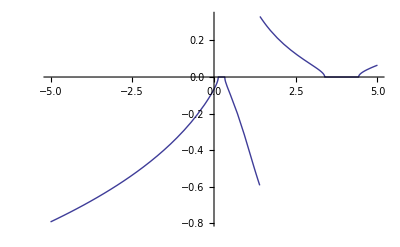

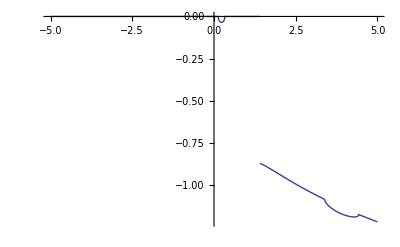

```mathematica
inlist={Lambda1->1,Lambda2->2.5,Lambda3->-2.6,Lambda4->-2.7,Lambda5->0.001,mh->125.09,v->246,mH->500};
sol[[5,1]]/.inlist//Simplify
```

```mathematica
?Plot3D
```

Plot3D[f,{x,x_min,x_max},{y,y_min,y_max}] generates a three-dimensional plot of f as a function of x and y. 
Plot3D[{f_1,f_2,…},{x,x_min,x_max},{y,y_min,y_max}] plots several functions.

```mathematica
FindInstance[(tanb/.sol[[1,1]]/.{mh->125.09,v->246})>0,{Lambda1,Lambda2,Lambda3,Lambda4,Lambda5,mH}]
```

$Aborted

```mathematica
?FindInstance
```

FindInstance[expr,vars] finds an instance of vars that makes the statement expr be True. 
FindInstance[expr,vars,dom] finds an instance over the domain dom. Common choices of dom are Complexes, Reals, Integers, and Booleans. 
FindInstance[expr,vars,dom,n] finds n instances.

```mathematica
Table[
inlist={Lambda1->1,Lambda2->2.5,Lambda3->-2.6,Lambda4->-2.7,Lambda5->0.001,mh->125.09,v->246,mH->500};
solx=tanb/.sol[[num,1]]/.Lambda1->x/.Lambda2->y/.inlist;
Print[num];
Plot3D[Im[solx],{x,-5,5},{y,-5,5}(*,PlotStyle->{Dashed,Black}*)]//Print;
,
{num,5,8}]
```

5

Power::infy: Infinite expression 1/0.^1/3 encountered.

-Graphics3D-

6

Power::infy: Infinite expression 1/0.^1/3 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

-Graphics3D-

7

-Graphics3D-

8

-Graphics3D-

{Null,Null,Null,Null}

```mathematica
inlist={Lambda1->1,Lambda2->4,Lambda3->-5.0,Lambda4->-4.0,Lambda5->0.001,mh->125.09,v->246,tana->Tan[-Pi/2-0.005]};
(sol1[[3]]/.inlist)
```

{tanb→0.435823-2.84217×10^-14 ⅈ,mH→-3.09814×10^-13+613.103 ⅈ,M12→197499.-1.30765×10^-8 ⅈ,mHp→3.26798×10^-13-646.712 ⅈ,mA→-2.0803×10^-13+734.37 ⅈ}

```mathematica
sys={Lambda1<4,Lambda2<4,Lambda3<4,Lambda4<4,Lambda5<0.001}
Reduce[sys/.sol1[[1]]]
```

{Lambda1<4,Lambda2<4,Lambda3<4,Lambda4<4,Lambda5<0.001}

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Lambda3<4.&&Lambda4<4.&&Lambda2<4.&&Lambda5<0.001&&Lambda1<4.

```mathematica
?Maximize
```

RowBox[{"Maximize", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["x", "TI"]}], "]"}] maximizes StyleBox["f", "TI"] with respect to StyleBox["x", "TI"].
RowBox[{"Maximize", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] maximizes StyleBox["f", "TI"] with respect to StyleBox["x", "TI"], StyleBox["y", "TI"], …. 
RowBox[{"Maximize", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["f", "TI"], ",", StyleBox["cons", "TI"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] maximizes StyleBox["f", "TI"] subject to the constraints StyleBox["cons", "TI"]. 
RowBox[{"Maximize", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["f", "TI"], ",", StyleBox["cons", "TI"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["dom", "TI"]}], "]"}] maximizes with variables over the domain StyleBox["dom", "TI"], typically Reals or Integers.

```mathematica
Minimize[{mHp/.sol1[[5]]/.mh->125.09/.v->246/.tana->1,0<Lambda1<4,0<Lambda2<4,-4<Lambda3<4,-4<Lambda4<4,0<Lambda5<0.01},{Lambda1,Lambda2,Lambda3,Lambda4,Lambda5}]
```

NMaximize::nrnum: The function value 0.  - 354.802\ ⅈ is not a real number at {Lambda1, Lambda2, Lambda3, Lambda4, Lambda5} = {3.69059, 2.28107, 1.10846, 3.98764, 0.00297885}.

Minimize[{-(√(-9.79378×10^8-3.7877×10^9 Lambda1+«48»+«1»-14648745024 Lambda2 Lambda5 (-(«1»)/(3 (-«19»+«1»))-(«1»)/(«1»)+(«1»)^(«1»)/(3 «1»«1»(«1»)))^2))/(√(-125180.+242064 Lambda1+242064 Lambda2+242064 Lambda3+242064 Lambda4+242064 Lambda5)),0<Lambda1<4,0<«7»<4,«1»,-4<Lambda4<4,0<Lambda5<0.01},«1»]

```mathematica
.
```

```mathematica
inlist={Lambda1->1,Lambda2->4,Lambda3->3.0,Lambda4->-4.0,Lambda5->0.001,mh->125.09,v->246,tana->Tan[+Pi/2-0.005]};
mHp/.sol1[[3]]/.inlist
mH/.sol1[[3]]/.inlist
```

241.186+3.16775×10^-13 ⅈ

-500.656-3.19397×10^-13 ⅈ

```mathematica
Reduce[Join[quarticmatchings/.Lambda1->0/.Lambda2->0/.Lambda3->0/.Lambda4->0/.Lambda5->0,{(*mH>0&&mHp>0&&mA>0*)}]]
```

((tanb==-ⅈ||tanb==ⅈ)&&mHp==0&&mA==0&&v+tana^2 v≠0)||(tana==tanb&&mH==0&&(mh==-mHp||mh==mHp)&&(mA==-mHp||mA==mHp)&&1+tanb^2≠0&&M12==-(mHp^2 tanb)/(1+tanb^2)&&tanb v≠0)||((tanb==-ⅈ||tanb==ⅈ)&&mHp==0&&(mh==-ⅈ mH||mh==ⅈ mH)&&mA==0&&1+tana^2≠0&&M12==(mH^2 tanb-mH^2 tana^2 tanb)/(1+tana^2)&&v≠0)||(mHp==0&&1+tanb^2≠0&&mH==0&&mh==0&&mA==0&&1+tana^2≠0&&M12==0&&tana tanb v-tanb^2 v+tana^2 tanb^2 v-tana tanb^3 v≠0)||(tanb≠0&&tana==-1/tanb&&tana-tanb≠0&&(mH==-mHp||mH==mHp)&&(mh==-√(-mH^2+mHp^2)||mh==√(-mH^2+mHp^2))&&(mA==-mHp||mA==mHp)&&M12==mH^2/(tana-tanb)&&v≠0)

```mathematica
quarticmatchings/.tana->-1/tanb//Simplify
```

{Lambda1==(mh^2+tanb (M12+mH^2 tanb+M12 tanb^2))/(2 v^2),Lambda2==(M12+mH^2 tanb+M12 tanb^2+mh^2 tanb^3)/(2 tanb^3 v^2),Lambda3==(M12+mh^2 tanb-mH^2 tanb+2 mHp^2 tanb+M12 tanb^2)/(tanb v^2),Lambda4==-(M12-mA^2 tanb+2 mHp^2 tanb+M12 tanb^2)/(tanb v^2),Lambda5==-(M12+mA^2 tanb+M12 tanb^2)/(tanb v^2)}

```mathematica
x=Get["~/_work/IntoSMASH/vacuumstab/jonastabs"];
x//Length
```

3

```mathematica
x[[3]]//Length
```

111

```mathematica
good=Cases[x[[3]],{___,complete->1,___}];
good//Length
```

30

```mathematica
{mA-mHp,mH-mHp,M12-mH^2/(tana-tanb),tana+1/tanb,Sqrt[-mH^2+mHp^2]}/.good
```

{{-35.104,24.755,51062.6,0.118944,0.+179.217 ⅈ},{5.576,56.959,28571.,-0.0328799,0.+278.32 ⅈ},{-41.917,-34.54,5396.02,0.0214231,198.209},{-45.085,-5.262,34550.,0.0272929,92.7617},{2.435,77.877,58392.7,0.0905204,0.+317.052 ⅈ},{-70.639,-8.329,58769.5,0.110577,111.713},{-3.942,78.126,60638.7,0.043402,0.+325.567 ⅈ},{-62.367,-57.196,6119.37,0.011866,315.601},{-103.859,-49.82,31135.9,0.0476013,242.008},{-52.333,-57.519,-196.07,0.0575234,279.586},{18.573,23.148,1482.21,0.0110675,0.+171.75 ⅈ},{-29.048,-30.256,783.754,0.0221785,210.799},{-7.169,55.212,54723.1,0.0162303,0.+305.395 ⅈ},{-89.638,-44.551,20269.9,-0.0510086,247.035},{-5.518,14.648,10775.5,-0.00339064,0.+137.494 ⅈ},{-66.509,-45.855,7936.49,-0.0511111,251.887},{-76.622,-48.784,22155.3,0.0965419,240.31},{-45.28,25.859,43780.4,-0.039864,0.+197.503 ⅈ},{-53.372,24.036,41082.,-0.076021,0.+182.164 ⅈ},{-18.032,1.156,22428.,0.0169175,0.+47.9147 ⅈ},{-42.619,-37.237,944.29,-0.0236173,230.306},{-53.584,-7.923,34948.8,-0.027033,121.503},{-38.381,31.136,41797.3,-0.010385,0.+200.111 ⅈ},{4.787,31.745,27444.,0.038986,0.+223.082 ⅈ},{-58.913,-48.557,9539.21,0.0569609,234.185},{-64.607,3.551,35633.,-0.0893376,0.+73.8593 ⅈ},{-39.657,-37.779,440.639,-0.00564718,271.207},{-10.99,7.561,6469.95,-0.0510494,0.+109.806 ⅈ},{-87.792,-10.933,75721.4,0.196418,124.491},{-1.057,-4.194,-109.208,0.0329159,77.1609}}

```mathematica
quarticmatchings
```

{Lambda1==((1+tanb^2) (mH^2+M12 tanb+tana^2 (mh^2+M12 tanb)))/(2 (1+tana^2) v^2),Lambda2==((M12+M12 tana^2+(mh^2+mH^2 tana^2) tanb) (1+tanb^2))/(2 (1+tana^2) tanb^3 v^2),Lambda3==(-mh^2 tana+2 mHp^2 (1+tana^2) tanb-mh^2 tana tanb^2+mH^2 tana (1+tanb^2)+M12 (1+tana^2) (1+tanb^2))/((1+tana^2) tanb v^2),Lambda4==(-M12+mA^2 tanb-2 mHp^2 tanb-M12 tanb^2)/(tanb v^2),Lambda5==(-M12-mA^2 tanb-M12 tanb^2)/(tanb v^2)}